```mathematica
Solve[a x+y==7&&b x-y==1,{x,y}]
```

```mathematica
Solve[mu==B/(B-1) && var==A^2B/((B-2)(B-1)^2),{A,B}]
```

{{A→-(√(2 var-mu var))/(√(mu-2 mu^2+mu^3)),B→mu/(-1+mu)},{A→(√(2 var-mu var))/(√(mu-2 mu^2+mu^3)),B→mu/(-1+mu)}}

```mathematica
f[x_,p_]:=1/x(x+Sqrt[x(p+x)])
```

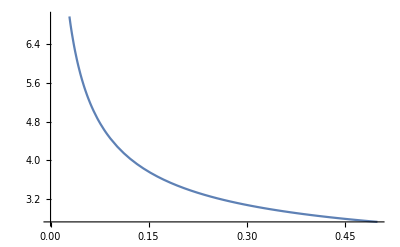

```mathematica
Plot[f[x,1],{x,0,0.5}]
```

```mathematica
g1[x_,p_]:=1/x(x^2+p+Sqrt[p(x^2+p)])
```

```mathematica
g2[x_,p_]:=1/x(x^2+p-Sqrt[p(x^2+p)])
```

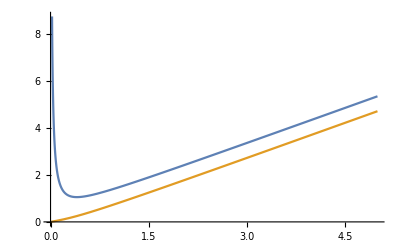

```mathematica
Plot[{g1[x,0.1],g2[x,0.1]},{x,0,5}]
```

```mathematica
Solve[mean==lambda/(alpha-1)+1 && var==lambda^2alpha/((alpha-2)(alpha-1)^2),{lambda,alpha}]
```

{{lambda→-((-1+mean) (1-2 mean+mean^2+var))/(1-2 mean+mean^2-var),alpha→(2 var)/(-1+2 mean-mean^2+var)}}